## Vykreslování grafů pro nově vygenerovaná data

## Výběr dat

🐺 Zde je potřeba vybrat složku a nazvy souboru k vygenerování

```mathematica
𝕊aveFolder="test";  (*složka s uloženými daty*)
𝔽ileNames={"test"};  (*názvy souborů*)
```

## Graf: autokorelační funkce

### Zpracovani dat

```mathematica
𝔾raphs=ConstantArray[0,1];

𝕋able=ConstantArray[0,1];
𝕋ableBoundaryCondition=ConstantArray[0,1];
```

#### Import dat

```mathematica
nn=Length[𝔽ileNames];

suffix={"_c_t.dat","_log.dat","_BC.dat","_error.dat"}; (*přípony souborů*)


(*Import příslušných dat*)
𝔻ataNumericalSolution=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>"/"<>𝔽ileNames[[i]]<>suffix[[1]]][[2;;]],{i,1,nn}];
𝔻ataBC=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>"/"<>𝔽ileNames[[i]]<>suffix[[3]]][[2;;]],{i,1,nn}];

𝔻ataLog=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>"/"<>𝔽ileNames[[i]]<>suffix[[2]]],{i,1,nn}];
```

#### Vygenerování grafu: Autokorelační funkce

```mathematica
(*----- Nastavení-----*)
ℙlotRange=All;

𝔽ontSize=12; 
𝕀mageSize=400;
tt=0.0015;(*tloušťka čar*)

ℂolours={Red,Blue,Darker[Green],Magenta,Black,Darker[Cyan]};
𝔾raphNumber=1;


nn2=Length[ℂolours];
(*Popisky grafu*)
ℙlotLabel="Časový vývoj autokorelační funkce";
ℙlotLegends={"Graf 1: Re(c(t))","Graf 1: Im(c(t))","Graf 2: Re(c(t))","Graf 2: Im(c(t))","Graf 3: Re(c(t))","Graf 3: Im(c(t))"}[[;;2*nn]];
𝔽rameLabel={Style["t",𝔽ontSize],Rotate[Style["c(t)",𝔽ontSize],-π/2]};
ℙlotData=ConstantArray[0,2*nn]; (*pomocné pole pro uložení dat, které se budou vynášet do grafu*)

(*----- Data -----*)
(* Numerické řešení*)
For[i=1,i<=nn,i++,
ℙlotData[[2*i-1]]=𝔻ataNumericalSolution[[i]][[;;,{1,2}]];
ℙlotData[[2*i]]=𝔻ataNumericalSolution[[i]][[;;,{1,3}]];
];
(*----- Vygenerování grafu -----*)
(*Plotstyle*)
𝕃ineStyle=ConstantArray[0,2*nn2];
For[i=1,i<=nn2/2,i++,
𝕃ineStyle[[2*i-1]]={ℂolours[[2*i-1]],Thickness[tt]};
𝕃ineStyle[[2*i]]={ℂolours[[2*i]],Thickness[tt],Dashed};
]

(*Legenda*)
𝕃ineLegend=ConstantArray[0,2*nn2];
For[i=1,i<=nn2/2,i++,
𝕃ineLegend[[2*i-1]]=ℂolours[[2*i-1]];
𝕃ineLegend[[2*i]]={ℂolours[[2*i]],Dashed};
]
𝕃ineLegend=LineLegend[𝕃ineLegend,ℙlotLegends];

(*Výsledný graf*)
𝔾raphs[[𝔾raphNumber]]=ListPlot[ℙlotData,PlotRange->ℙlotRange,Joined->True,PlotStyle->𝕃ineStyle,PlotLegends->𝕃ineLegend,PlotLabel->ℙlotLabel,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,ImageSize->𝕀mageSize];
```

#### Tabulka: Parametry numerického výpočtu

```mathematica
(*----- Nastavení -----*)
𝕋ableNumber=1; (*index grafu*)
𝕊howColumns={1,2,3,4,5,6,7,8,9,10,11,12,13,14}; (*sloupce, které chceme zobrazit*)

(*----- Automatické vytvoření tabulky -----*)
ℍeader={{Null,"h","N=n+1","x_0","x_n","Δt","t_steps","μ","ω","x_(0, Gauss)","p_(0, Gauss)","σ","n_HO","runtime(s)"}}; (*hlavička (popisky sloupců)*)
(*𝔻ividers=All;*)
𝔻ividers={{{True}},{True,True,{False},True}};(*{{{True}}=v každém sloupečku je |; {True=0.řádek,True=1.řádek,{False}=všechny řádky mezi předchozím řádkem a řádkem, který odpovídá následujícímu příkazu,True=poslední řádek (číslujeme od konce)}}*)
𝔹ackground=None;
(*Vyčtení dat z log souboru*)
hLog=Table[𝔻ataLog[[i,1,2]],{i,1,nn}];
NLog=Table[𝔻ataLog[[i,2,2]],{i,1,nn}];
x0Log=Table[𝔻ataLog[[i,3,2]],{i,1,nn}];
xnLog=Table[𝔻ataLog[[i,4,2]],{i,1,nn}];
dtLog=Table[𝔻ataLog[[i,5,2]],{i,1,nn}];
tstepsLog=Table[𝔻ataLog[[i,6,2]],{i,1,nn}];
μLog=Table[𝔻ataLog[[i,7,2]],{i,1,nn}];
ωLog=Table[𝔻ataLog[[i,8,2]],{i,1,nn}];
x0GaussLog=Table[𝔻ataLog[[i,9,2]],{i,1,nn}];
p0Log=Table[𝔻ataLog[[i,10,2]],{i,1,nn}];
σLog=Table[𝔻ataLog[[i,11,2]],{i,1,nn}];
nHermiteLog=Table[𝔻ataLog[[i,12,2]],{i,1,nn}];
runtimeLog=Table[𝔻ataLog[[i,13,2]],{i,1,nn}];

temp=Table[{"Graf "<>ToString[i],hLog[[i]],NLog[[i]],x0Log[[i]],xnLog[[i]],dtLog[[i]],tstepsLog[[i]],μLog[[i]],ωLog[[i]],x0GaussLog[[i]],p0Log[[i]],σLog[[i]],nHermiteLog[[i]],runtimeLog[[i]]},{i,1,nn}];(*vytvoření tabulky s daty*)
temp=Join[ℍeader,temp];(*připojení hlavičky*)
temp=temp[[;;,𝕊howColumns]];(*výběr požadovaných sloupečků*)

𝕋able[[𝕋ableNumber]]=Grid[temp,Dividers->𝔻ividers,Background->𝔹ackground];(*výsledná tabulka*)
```

#### Tabulka: Splnění okrajové podmínky

```mathematica
(*----- Nastavení -----*)
𝕋ableBCNumber=1;

(*----- Automatické vytvoření tabulky -----*)
ℍeader={{ Null,"Max|Re(ψ(x_0,t))|","Max|Im(ψ(x_0,t))|","Max|Re(ψ(x_n,t))|","Max|Im(ψ(x_n,t))|"}};
𝔻ividers={{{True}},{True,True,{False},True}};
𝔹ackground=None;
(*Pole pro ukládání hodnot velikostí vlnové funkce na okraji gridu*)
𝕄axAbsReψx0=ConstantArray[0,nn];
𝕄axAbsImψx0=ConstantArray[0,nn];
𝕄axAbsReψxn=ConstantArray[0,nn];
𝕄axAbsImψxn=ConstantArray[0,nn];

(*Nalezení největší hodonoty (v absolutní hodnotě)*)
For[i=1,i<=nn,i++,
𝕄axAbsReψx0[[i]]=Max[Abs[𝔻ataBC[[i]][[;;,2]]]];
𝕄axAbsImψx0[[i]]=Max[Abs[𝔻ataBC[[i]][[;;,3]]]];
𝕄axAbsReψxn[[i]]=Max[Abs[𝔻ataBC[[i]][[;;,4]]]];
𝕄axAbsImψxn[[i]]=Max[Abs[𝔻ataBC[[i]][[;;,5]]]];
]

(*Vytvoření tabulky*)
temp=Table[{"Graf "<>ToString[i],𝕄axAbsReψx0[[i]],𝕄axAbsImψx0[[i]],𝕄axAbsReψxn[[i]],𝕄axAbsImψxn[[i]]},{i,1,nn}];
temp=Join[ℍeader,temp];

𝕋ableBoundaryCondition[[𝕋ableBCNumber]]=Grid[temp,Dividers->𝔻ividers,Background->𝔹ackground];
```

### Graf

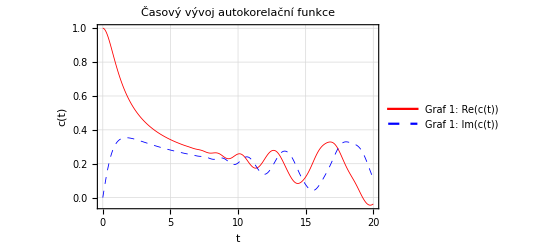

| h | N=n+1 | x_0 | x_n | Δt | t_steps | μ | ω | x_(0, Gauss) | p_(0, Gauss) | σ | n_HO | runtime(s)
Graf 1 | 0.05 | 512 | -12.775 | 12.775 | 0.01 | 2000 | 1 | 1.5 | -5 | 0 | 0.5 | 0 | 16.5303

| Max|Re(ψ(x_0,t))| | Max|Im(ψ(x_0,t))| | Max|Re(ψ(x_n,t))| | Max|Im(ψ(x_n,t))|
Graf 1 | 0.213154 | 0.25953 | 0.222298 | 0.256174

```mathematica
𝔾raphs[[1]]
𝕋able[[1]]
𝕋ableBoundaryCondition[[1]]
```

## Graf: Chyba numerického řešení

### Zpracování dat

```mathematica
𝔾raphsAcc=ConstantArray[0,1];
```

#### Import dat

```mathematica
nn=Length[𝔽ileNames];

suffix={"_c_t.dat","_log.dat","_BC.dat","_error.dat"}; (*přípony souborů*)


(*Import příslušných dat*)
𝔻ataError=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>"/"<>𝔽ileNames[[i]]<>suffix[[4]]][[2;;]],{i,1,nn}];
```

#### Vygenerování grafu: Chyba numerického řešení

```mathematica
(*----- Nastavení-----*)
𝔾raphAccNumber=1;
ℙlotRange=All;

𝔽ontSize=12; 
𝕀mageSize=400;
tt=0.0015;(*tloušťka čar*)
ℂolours={Red,Blue,Darker[Green],Magenta,Black,Darker[Cyan]};
nn2=Length[ℂolours];
(*Popisky grafu*)
ℙlotLabel="Vývoj chyby numerického řešení";
ℙlotLegends={"Graf 1","Graf 2","Graf 3","Graf 4","Graf 5","Graf 6"}[[;;nn]];
(*𝔽rameLabel={Style["t",𝔽ontSize],Rotate[Style["Max|ψ_num(x,t)-ψ_exact(x,t)|",𝔽ontSize],-π/2]};*)
𝔽rameLabel={Style["t",𝔽ontSize],Style["Max|ψ_num(x,t)-ψ_exact(x,t)|",𝔽ontSize]};
(*----- Data -----*)
(* Chyba numerického řešení*)
ℙlotData=𝔻ataError;
(*----- Vygenerování grafu -----*)
(*Plotstyle*)
𝕃ineStyle=ConstantArray[0,nn2];
For[i=1,i<=nn,i++,
𝕃ineStyle[[i]]={ℂolours[[i]],Thickness[tt]};
]

(*Legenda*)
𝕃ineLegend=ConstantArray[0,nn2];
For[i=1,i<=nn,i++,
𝕃ineLegend[[i]]=ℂolours[[i]];
]
𝕃ineLegend=LineLegend[𝕃ineLegend,ℙlotLegends];

(*Výsledný graf*)
𝔾raphsAcc[[𝔾raphAccNumber]]=ListLogPlot[ℙlotData,PlotRange->ℙlotRange,Joined->True,PlotStyle->𝕃ineStyle,PlotLegends->𝕃ineLegend,PlotLabel->ℙlotLabel,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,ImageSize->𝕀mageSize];
```

### Graf

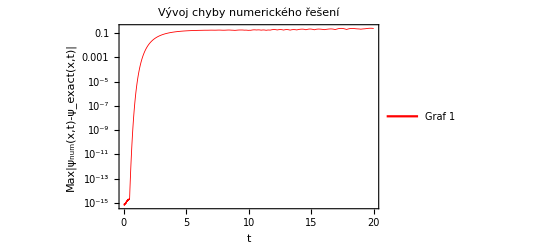

```mathematica
𝔾raphsAcc[[1]]
```